Initializing

```mathematica
Unprotect[DirectedInfinity];
DirectedInfinity/:Log[0] 0.:=0;
DirectedInfinity/:Log[0] 0:=0;
Protect[DirectedInfinity];
Unprotect[Times];
Unprotect[Indeterminate];
Times/:Times[0,Indeterminate]:=0;
Times/:Times[0.,Indeterminate]:=0;
Indeterminate/:Indeterminate*0:=0
Indeterminate/:Indeterminate*0.:=0
Protect[Indeterminate];
Protect[Times];
```

```mathematica
Q[t_]:=(adad[t] aa[t] + ada[t] ada[t] + ada[t] ada[t] - 2 ad[t] ad[t] a[t] a[t])/ada[t]-ada[t]
```

## Solving: two-mode model

```mathematica
stringequations3 = {"a'[t] == -0.5 γ1( a[t]) + -I σ1( a[t]) + -I σ3( a[t]) + (-2 I) σ1( ad[t] aa[t] + a[t] ada[t] + a[t] ada[t] - 2 ad[t] a[t] a[t]) + (-2 I) σ5( ad[t] ab[t] + a[t] adb[t] + b[t] ada[t] - 2 ad[t] a[t] b[t]) + (-2 I) σ4( ad[t] bb[t] + b[t] adb[t] + b[t] adb[t] - 2 ad[t] b[t] b[t]) + -I σ5( bd[t] aa[t] + a[t] bda[t] + a[t] bda[t] - 2 bd[t] a[t] a[t]) + -I σ2( bd[t] ab[t] + a[t] bdb[t] + b[t] bda[t] - 2 bd[t] a[t] b[t]) + I σ5( bd[t] bb[t] + b[t] bdb[t] + b[t] bdb[t] - 2 bd[t] b[t] b[t])","ad'[t] == -0.5 γ1( ad[t]) + I σ1( ad[t]) + I σ3( ad[t]) + (2 I) σ1( ad[t] ada[t] + ad[t] ada[t] + a[t] adad[t] - 2 ad[t] ad[t] a[t]) + I σ5( ad[t] adb[t] + ad[t] adb[t] + b[t] adad[t] - 2 ad[t] ad[t] b[t]) + (2 I) σ5( ad[t] bda[t] + bd[t] ada[t] + a[t] adbd[t] - 2 ad[t] bd[t] a[t]) + I σ2( ad[t] bdb[t] + bd[t] adb[t] + b[t] adbd[t] - 2 ad[t] bd[t] b[t]) + (2 I) σ4( bd[t] bda[t] + bd[t] bda[t] + a[t] bdbd[t] - 2 bd[t] bd[t] a[t]) + -I σ5( bd[t] bdb[t] + bd[t] bdb[t] + b[t] bdbd[t] - 2 bd[t] bd[t] b[t])","b'[t] == -0.5 γ2( b[t]) + -I σ1( b[t]) + -I σ3( b[t]) + -I σ5( ad[t] aa[t] + a[t] ada[t] + a[t] ada[t] - 2 ad[t] a[t] a[t]) + -I σ2( ad[t] ab[t] + a[t] adb[t] + b[t] ada[t] - 2 ad[t] a[t] b[t]) + I σ5( ad[t] bb[t] + b[t] adb[t] + b[t] adb[t] - 2 ad[t] b[t] b[t]) + (-2 I) σ4( bd[t] aa[t] + a[t] bda[t] + a[t] bda[t] - 2 bd[t] a[t] a[t]) + (2 I) σ5( bd[t] ab[t] + a[t] bdb[t] + b[t] bda[t] - 2 bd[t] a[t] b[t]) + (-2 I) σ1( bd[t] bb[t] + b[t] bdb[t] + b[t] bdb[t] - 2 bd[t] b[t] b[t])","bd'[t] == -0.5 γ2( bd[t]) + I σ1( bd[t]) + I σ3( bd[t]) + I σ5( ad[t] ada[t] + ad[t] ada[t] + a[t] adad[t] - 2 ad[t] ad[t] a[t]) + (2 I) σ4( ad[t] adb[t] + ad[t] adb[t] + b[t] adad[t] - 2 ad[t] ad[t] b[t]) + I σ2( ad[t] bda[t] + bd[t] ada[t] + a[t] adbd[t] - 2 ad[t] bd[t] a[t]) + (-2 I) σ5( ad[t] bdb[t] + bd[t] adb[t] + b[t] adbd[t] - 2 ad[t] bd[t] b[t]) + -I σ5( bd[t] bda[t] + bd[t] bda[t] + a[t] bdbd[t] - 2 bd[t] bd[t] a[t]) + (2 I) σ1( bd[t] bdb[t] + bd[t] bdb[t] + b[t] bdbd[t] - 2 bd[t] bd[t] b[t])","aa'[t] == -1. γ1( aa[t]) + (-4 I) σ1( aa[t]) + (-2 I) σ3( aa[t]) + (-2 I) σ5( ab[t]) + (-2 I) σ4( bb[t]) + (-4 I) σ1( ada[t] aa[t] + ada[t] aa[t] + ada[t] aa[t] - 2 ad[t] a[t] a[t] a[t]) + (-4 I) σ5( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + (-4 I) σ4( ada[t] bb[t] + adb[t] ab[t] + adb[t] ab[t] - 2 ad[t] a[t] b[t] b[t]) + (-2 I) σ5( bda[t] aa[t] + bda[t] aa[t] + bda[t] aa[t] - 2 bd[t] a[t] a[t] a[t]) + (-2 I) σ2( bda[t] ab[t] + bda[t] ab[t] + bdb[t] aa[t] - 2 bd[t] a[t] a[t] b[t]) + (2 I) σ5( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t])","ada'[t] == -1. γ1( ada[t]) + -I σ5( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (-2 I) σ4( adad[t] bb[t] + adb[t] adb[t] + adb[t] adb[t] - 2 ad[t] ad[t] b[t] b[t]) + I σ5( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + I σ5( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (2 I) σ4( bdbd[t] aa[t] + bda[t] bda[t] + bda[t] bda[t] - 2 bd[t] bd[t] a[t] a[t]) + -I σ5( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t])","adad'[t] == -1. γ1( adad[t]) + (4 I) σ1( adad[t]) + (2 I) σ3( adad[t]) + (2 I) σ5( adbd[t]) + (2 I) σ4( bdbd[t]) + (4 I) σ1( adad[t] ada[t] + adad[t] ada[t] + ada[t] adad[t] - 2 ad[t] ad[t] ad[t] a[t]) + (2 I) σ5( adad[t] adb[t] + adad[t] adb[t] + adb[t] adad[t] - 2 ad[t] ad[t] ad[t] b[t]) + (4 I) σ5( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + (2 I) σ2( adad[t] bdb[t] + adbd[t] adb[t] + adb[t] adbd[t] - 2 ad[t] ad[t] bd[t] b[t]) + (4 I) σ4( adbd[t] bda[t] + adbd[t] bda[t] + ada[t] bdbd[t] - 2 ad[t] bd[t] bd[t] a[t]) + (-2 I) σ5( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t])","bb'[t] == (-2 I) σ4( aa[t]) + (2 I) σ5( ab[t]) + -1. γ2( bb[t]) + (-4 I) σ1( bb[t]) + (-2 I) σ3( bb[t]) + (-2 I) σ5( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + (-2 I) σ2( ada[t] bb[t] + adb[t] ab[t] + adb[t] ab[t] - 2 ad[t] a[t] b[t] b[t]) + (2 I) σ5( adb[t] bb[t] + adb[t] bb[t] + adb[t] bb[t] - 2 ad[t] b[t] b[t] b[t]) + (-4 I) σ4( bda[t] ab[t] + bda[t] ab[t] + bdb[t] aa[t] - 2 bd[t] a[t] a[t] b[t]) + (4 I) σ5( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t]) + (-4 I) σ1( bdb[t] bb[t] + bdb[t] bb[t] + bdb[t] bb[t] - 2 bd[t] b[t] b[t] b[t])","bdb'[t] == -1. γ2( bdb[t]) + I σ5( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (2 I) σ4( adad[t] bb[t] + adb[t] adb[t] + adb[t] adb[t] - 2 ad[t] ad[t] b[t] b[t]) + -I σ5( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + -I σ5( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (-2 I) σ4( bdbd[t] aa[t] + bda[t] bda[t] + bda[t] bda[t] - 2 bd[t] bd[t] a[t] a[t]) + I σ5( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t])","bdbd'[t] == (2 I) σ4( adad[t]) + (-2 I) σ5( adbd[t]) + -1. γ2( bdbd[t]) + (4 I) σ1( bdbd[t]) + (2 I) σ3( bdbd[t]) + (2 I) σ5( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + (4 I) σ4( adad[t] bdb[t] + adbd[t] adb[t] + adb[t] adbd[t] - 2 ad[t] ad[t] bd[t] b[t]) + (2 I) σ2( adbd[t] bda[t] + adbd[t] bda[t] + ada[t] bdbd[t] - 2 ad[t] bd[t] bd[t] a[t]) + (-4 I) σ5( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t]) + (-2 I) σ5( bdbd[t] bda[t] + bdbd[t] bda[t] + bda[t] bdbd[t] - 2 bd[t] bd[t] bd[t] a[t]) + (4 I) σ1( bdbd[t] bdb[t] + bdbd[t] bdb[t] + bdb[t] bdbd[t] - 2 bd[t] bd[t] bd[t] b[t])","ab'[t] == -I σ5( aa[t]) + -0.5 γ1( ab[t]) + -0.5 γ2( ab[t]) + (-2 I) σ1( ab[t]) + -I σ2( ab[t]) + (-2 I) σ3( ab[t]) + I σ5( bb[t]) + -I σ5( ada[t] aa[t] + ada[t] aa[t] + ada[t] aa[t] - 2 ad[t] a[t] a[t] a[t]) + (-2 I) σ1( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + -I σ2( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + -I σ5( ada[t] bb[t] + adb[t] ab[t] + adb[t] ab[t] - 2 ad[t] a[t] b[t] b[t]) + (-2 I) σ4( adb[t] bb[t] + adb[t] bb[t] + adb[t] bb[t] - 2 ad[t] b[t] b[t] b[t]) + (-2 I) σ4( bda[t] aa[t] + bda[t] aa[t] + bda[t] aa[t] - 2 bd[t] a[t] a[t] a[t]) + I σ5( bda[t] ab[t] + bda[t] ab[t] + bdb[t] aa[t] - 2 bd[t] a[t] a[t] b[t]) + (-2 I) σ1( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t]) + -I σ2( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t]) + I σ5( bdb[t] bb[t] + bdb[t] bb[t] + bdb[t] bb[t] - 2 bd[t] b[t] b[t] b[t])","adb'[t] == -0.5 γ1( adb[t]) + -0.5 γ2( adb[t]) + -I σ5( adad[t] aa[t] + ada[t] ada[t] + ada[t] ada[t] - 2 ad[t] ad[t] a[t] a[t]) + (2 I) σ1( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + -I σ2( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (2 I) σ5( adad[t] bb[t] + adb[t] adb[t] + adb[t] adb[t] - 2 ad[t] ad[t] b[t] b[t]) + (-2 I) σ4( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + (4 I) σ5( adbd[t] ab[t] + ada[t] bdb[t] + adb[t] bda[t] - 2 ad[t] bd[t] a[t] b[t]) + (-2 I) σ1( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + I σ2( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (2 I) σ4( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + -I σ5( bdbd[t] bb[t] + bdb[t] bdb[t] + bdb[t] bdb[t] - 2 bd[t] bd[t] b[t] b[t])","bda'[t] == -0.5 γ1( bda[t]) + -0.5 γ2( bda[t]) + I σ5( adad[t] aa[t] + ada[t] ada[t] + ada[t] ada[t] - 2 ad[t] ad[t] a[t] a[t]) + (2 I) σ4( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (-2 I) σ1( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + I σ2( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + (-4 I) σ5( adbd[t] ab[t] + ada[t] bdb[t] + adb[t] bda[t] - 2 ad[t] bd[t] a[t] b[t]) + (-2 I) σ4( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (-2 I) σ5( bdbd[t] aa[t] + bda[t] bda[t] + bda[t] bda[t] - 2 bd[t] bd[t] a[t] a[t]) + (2 I) σ1( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + -I σ2( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + I σ5( bdbd[t] bb[t] + bdb[t] bdb[t] + bdb[t] bdb[t] - 2 bd[t] bd[t] b[t] b[t])","adbd'[t] == I σ5( adad[t]) + -0.5 γ1( adbd[t]) + -0.5 γ2( adbd[t]) + (2 I) σ1( adbd[t]) + I σ2( adbd[t]) + (2 I) σ3( adbd[t]) + -I σ5( bdbd[t]) + I σ5( adad[t] ada[t] + adad[t] ada[t] + ada[t] adad[t] - 2 ad[t] ad[t] ad[t] a[t]) + (2 I) σ4( adad[t] adb[t] + adad[t] adb[t] + adb[t] adad[t] - 2 ad[t] ad[t] ad[t] b[t]) + (2 I) σ1( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + I σ2( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + -I σ5( adad[t] bdb[t] + adbd[t] adb[t] + adb[t] adbd[t] - 2 ad[t] ad[t] bd[t] b[t]) + I σ5( adbd[t] bda[t] + adbd[t] bda[t] + ada[t] bdbd[t] - 2 ad[t] bd[t] bd[t] a[t]) + (2 I) σ1( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t]) + I σ2( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t]) + (2 I) σ4( bdbd[t] bda[t] + bdbd[t] bda[t] + bda[t] bdbd[t] - 2 bd[t] bd[t] bd[t] a[t]) + -I σ5( bdbd[t] bdb[t] + bdbd[t] bdb[t] + bdb[t] bdbd[t] - 2 bd[t] bd[t] bd[t] b[t])"};
```

```mathematica
stringequations2 = {"a'[t] == -0.5 γ1( a[t]) + I σ1( a[t]) + I σ3( a[t]) + (-2 I) σ5( b[t]) + (2 I) σ1( ad[t] aa[t] + a[t] ada[t] + a[t] ada[t] - 2 ad[t] a[t] a[t]) + (2 I) σ5( ad[t] ab[t] + a[t] adb[t] + b[t] ada[t] - 2 ad[t] a[t] b[t]) + (2 I) σ4( ad[t] bb[t] + b[t] adb[t] + b[t] adb[t] - 2 ad[t] b[t] b[t]) + I σ5( bd[t] aa[t] + a[t] bda[t] + a[t] bda[t] - 2 bd[t] a[t] a[t]) + I σ2( bd[t] ab[t] + a[t] bdb[t] + b[t] bda[t] - 2 bd[t] a[t] b[t]) + -I σ5( bd[t] bb[t] + b[t] bdb[t] + b[t] bdb[t] - 2 bd[t] b[t] b[t])","ad'[t] == -0.5 γ1( ad[t]) + -I σ1( ad[t]) + -I σ3( ad[t]) + (-2 I) σ1( ad[t] ada[t] + ad[t] ada[t] + a[t] adad[t] - 2 ad[t] ad[t] a[t]) + -I σ5( ad[t] adb[t] + ad[t] adb[t] + b[t] adad[t] - 2 ad[t] ad[t] b[t]) + (-2 I) σ5( ad[t] bda[t] + bd[t] ada[t] + a[t] adbd[t] - 2 ad[t] bd[t] a[t]) + -I σ2( ad[t] bdb[t] + bd[t] adb[t] + b[t] adbd[t] - 2 ad[t] bd[t] b[t]) + (-2 I) σ4( bd[t] bda[t] + bd[t] bda[t] + a[t] bdbd[t] - 2 bd[t] bd[t] a[t]) + I σ5( bd[t] bdb[t] + bd[t] bdb[t] + b[t] bdbd[t] - 2 bd[t] bd[t] b[t])","b'[t] == -0.5 γ2( b[t]) + I σ1( b[t]) + I σ3( b[t]) + I σ5( ad[t] aa[t] + a[t] ada[t] + a[t] ada[t] - 2 ad[t] a[t] a[t]) + I σ2( ad[t] ab[t] + a[t] adb[t] + b[t] ada[t] - 2 ad[t] a[t] b[t]) + -I σ5( ad[t] bb[t] + b[t] adb[t] + b[t] adb[t] - 2 ad[t] b[t] b[t]) + (2 I) σ4( bd[t] aa[t] + a[t] bda[t] + a[t] bda[t] - 2 bd[t] a[t] a[t]) + (-2 I) σ5( bd[t] ab[t] + a[t] bdb[t] + b[t] bda[t] - 2 bd[t] a[t] b[t]) + (2 I) σ1( bd[t] bb[t] + b[t] bdb[t] + b[t] bdb[t] - 2 bd[t] b[t] b[t])","bd'[t] == -0.5 γ2( bd[t]) + -I σ1( bd[t]) + -I σ3( bd[t]) + (2 I) σ5( ad[t]) + -I σ5( ad[t] ada[t] + ad[t] ada[t] + a[t] adad[t] - 2 ad[t] ad[t] a[t]) + (-2 I) σ4( ad[t] adb[t] + ad[t] adb[t] + b[t] adad[t] - 2 ad[t] ad[t] b[t]) + -I σ2( ad[t] bda[t] + bd[t] ada[t] + a[t] adbd[t] - 2 ad[t] bd[t] a[t]) + (2 I) σ5( ad[t] bdb[t] + bd[t] adb[t] + b[t] adbd[t] - 2 ad[t] bd[t] b[t]) + I σ5( bd[t] bda[t] + bd[t] bda[t] + a[t] bdbd[t] - 2 bd[t] bd[t] a[t]) + (-2 I) σ1( bd[t] bdb[t] + bd[t] bdb[t] + b[t] bdbd[t] - 2 bd[t] bd[t] b[t])","aa'[t] == -1. γ1( aa[t]) + (4 I) σ1( aa[t]) + (2 I) σ3( aa[t]) + (-2 I) σ5( ab[t]) + (2 I) σ4( bb[t]) + (4 I) σ1( ada[t] aa[t] + ada[t] aa[t] + ada[t] aa[t] - 2 ad[t] a[t] a[t] a[t]) + (4 I) σ5( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + (4 I) σ4( ada[t] bb[t] + adb[t] ab[t] + adb[t] ab[t] - 2 ad[t] a[t] b[t] b[t]) + (2 I) σ5( bda[t] aa[t] + bda[t] aa[t] + bda[t] aa[t] - 2 bd[t] a[t] a[t] a[t]) + (2 I) σ2( bda[t] ab[t] + bda[t] ab[t] + bdb[t] aa[t] - 2 bd[t] a[t] a[t] b[t]) + (-2 I) σ5( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t])","ada'[t] == -1. γ1( ada[t]) + (-2 I) σ5( adb[t]) + I σ5( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (2 I) σ4( adad[t] bb[t] + adb[t] adb[t] + adb[t] adb[t] - 2 ad[t] ad[t] b[t] b[t]) + -I σ5( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + -I σ5( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (-2 I) σ4( bdbd[t] aa[t] + bda[t] bda[t] + bda[t] bda[t] - 2 bd[t] bd[t] a[t] a[t]) + I σ5( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t])","adad'[t] == -1. γ1( adad[t]) + (-4 I) σ1( adad[t]) + (-2 I) σ3( adad[t]) + (-2 I) σ5( adbd[t]) + (-2 I) σ4( bdbd[t]) + (-4 I) σ1( adad[t] ada[t] + adad[t] ada[t] + ada[t] adad[t] - 2 ad[t] ad[t] ad[t] a[t]) + (-2 I) σ5( adad[t] adb[t] + adad[t] adb[t] + adb[t] adad[t] - 2 ad[t] ad[t] ad[t] b[t]) + (-4 I) σ5( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + (-2 I) σ2( adad[t] bdb[t] + adbd[t] adb[t] + adb[t] adbd[t] - 2 ad[t] ad[t] bd[t] b[t]) + (-4 I) σ4( adbd[t] bda[t] + adbd[t] bda[t] + ada[t] bdbd[t] - 2 ad[t] bd[t] bd[t] a[t]) + (2 I) σ5( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t])","bb'[t] == (2 I) σ4( aa[t]) + (-2 I) σ5( ab[t]) + -1. γ2( bb[t]) + (4 I) σ1( bb[t]) + (2 I) σ3( bb[t]) + (2 I) σ5( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + (2 I) σ2( ada[t] bb[t] + adb[t] ab[t] + adb[t] ab[t] - 2 ad[t] a[t] b[t] b[t]) + (-2 I) σ5( adb[t] bb[t] + adb[t] bb[t] + adb[t] bb[t] - 2 ad[t] b[t] b[t] b[t]) + (4 I) σ4( bda[t] ab[t] + bda[t] ab[t] + bdb[t] aa[t] - 2 bd[t] a[t] a[t] b[t]) + (-4 I) σ5( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t]) + (4 I) σ1( bdb[t] bb[t] + bdb[t] bb[t] + bdb[t] bb[t] - 2 bd[t] b[t] b[t] b[t])","bdb'[t] == (2 I) σ5( adb[t]) + -1. γ2( bdb[t]) + -I σ5( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (-2 I) σ4( adad[t] bb[t] + adb[t] adb[t] + adb[t] adb[t] - 2 ad[t] ad[t] b[t] b[t]) + I σ5( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + I σ5( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (2 I) σ4( bdbd[t] aa[t] + bda[t] bda[t] + bda[t] bda[t] - 2 bd[t] bd[t] a[t] a[t]) + -I σ5( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t])","bdbd'[t] == (-2 I) σ4( adad[t]) + (6 I) σ5( adbd[t]) + -1. γ2( bdbd[t]) + (-4 I) σ1( bdbd[t]) + (-2 I) σ3( bdbd[t]) + (-2 I) σ5( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + (-4 I) σ4( adad[t] bdb[t] + adbd[t] adb[t] + adb[t] adbd[t] - 2 ad[t] ad[t] bd[t] b[t]) + (-2 I) σ2( adbd[t] bda[t] + adbd[t] bda[t] + ada[t] bdbd[t] - 2 ad[t] bd[t] bd[t] a[t]) + (4 I) σ5( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t]) + (2 I) σ5( bdbd[t] bda[t] + bdbd[t] bda[t] + bda[t] bdbd[t] - 2 bd[t] bd[t] bd[t] a[t]) + (-4 I) σ1( bdbd[t] bdb[t] + bdbd[t] bdb[t] + bdb[t] bdbd[t] - 2 bd[t] bd[t] bd[t] b[t])","ab'[t] == I σ5( aa[t]) + -0.5 γ1( ab[t]) + -0.5 γ2( ab[t]) + (2 I) σ1( ab[t]) + I σ2( ab[t]) + (2 I) σ3( ab[t]) + (-3 I) σ5( bb[t]) + I σ5( ada[t] aa[t] + ada[t] aa[t] + ada[t] aa[t] - 2 ad[t] a[t] a[t] a[t]) + (2 I) σ1( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + I σ2( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + I σ5( ada[t] bb[t] + adb[t] ab[t] + adb[t] ab[t] - 2 ad[t] a[t] b[t] b[t]) + (2 I) σ4( adb[t] bb[t] + adb[t] bb[t] + adb[t] bb[t] - 2 ad[t] b[t] b[t] b[t]) + (2 I) σ4( bda[t] aa[t] + bda[t] aa[t] + bda[t] aa[t] - 2 bd[t] a[t] a[t] a[t]) + -I σ5( bda[t] ab[t] + bda[t] ab[t] + bdb[t] aa[t] - 2 bd[t] a[t] a[t] b[t]) + (2 I) σ1( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t]) + I σ2( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t]) + -I σ5( bdb[t] bb[t] + bdb[t] bb[t] + bdb[t] bb[t] - 2 bd[t] b[t] b[t] b[t])","adb'[t] == -0.5 γ1( adb[t]) + -0.5 γ2( adb[t]) + I σ5( adad[t] aa[t] + ada[t] ada[t] + ada[t] ada[t] - 2 ad[t] ad[t] a[t] a[t]) + (-2 I) σ1( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + I σ2( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (-2 I) σ5( adad[t] bb[t] + adb[t] adb[t] + adb[t] adb[t] - 2 ad[t] ad[t] b[t] b[t]) + (2 I) σ4( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + (-4 I) σ5( adbd[t] ab[t] + ada[t] bdb[t] + adb[t] bda[t] - 2 ad[t] bd[t] a[t] b[t]) + (2 I) σ1( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + -I σ2( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (-2 I) σ4( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + I σ5( bdbd[t] bb[t] + bdb[t] bdb[t] + bdb[t] bdb[t] - 2 bd[t] bd[t] b[t] b[t])","bda'[t] == (2 I) σ5( ada[t]) + -0.5 γ1( bda[t]) + -0.5 γ2( bda[t]) + (-2 I) σ5( bdb[t]) + -I σ5( adad[t] aa[t] + ada[t] ada[t] + ada[t] ada[t] - 2 ad[t] ad[t] a[t] a[t]) + (-2 I) σ4( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (2 I) σ1( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + -I σ2( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + (4 I) σ5( adbd[t] ab[t] + ada[t] bdb[t] + adb[t] bda[t] - 2 ad[t] bd[t] a[t] b[t]) + (2 I) σ4( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (2 I) σ5( bdbd[t] aa[t] + bda[t] bda[t] + bda[t] bda[t] - 2 bd[t] bd[t] a[t] a[t]) + (-2 I) σ1( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + I σ2( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + -I σ5( bdbd[t] bb[t] + bdb[t] bdb[t] + bdb[t] bdb[t] - 2 bd[t] bd[t] b[t] b[t])","adbd'[t] == I σ5( adad[t]) + -0.5 γ1( adbd[t]) + -0.5 γ2( adbd[t]) + (-2 I) σ1( adbd[t]) + -I σ2( adbd[t]) + (-2 I) σ3( adbd[t]) + I σ5( bdbd[t]) + -I σ5( adad[t] ada[t] + adad[t] ada[t] + ada[t] adad[t] - 2 ad[t] ad[t] ad[t] a[t]) + (-2 I) σ4( adad[t] adb[t] + adad[t] adb[t] + adb[t] adad[t] - 2 ad[t] ad[t] ad[t] b[t]) + (-2 I) σ1( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + -I σ2( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + I σ5( adad[t] bdb[t] + adbd[t] adb[t] + adb[t] adbd[t] - 2 ad[t] ad[t] bd[t] b[t]) + -I σ5( adbd[t] bda[t] + adbd[t] bda[t] + ada[t] bdbd[t] - 2 ad[t] bd[t] bd[t] a[t]) + (-2 I) σ1( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t]) + -I σ2( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t]) + (-2 I) σ4( bdbd[t] bda[t] + bdbd[t] bda[t] + bda[t] bdbd[t] - 2 bd[t] bd[t] bd[t] a[t]) + I σ5( bdbd[t] bdb[t] + bdbd[t] bdb[t] + bdb[t] bdbd[t] - 2 bd[t] bd[t] bd[t] b[t])"};
```

```mathematica
(* Pump collective mode s_-. 
a = s_-
b = s_ +
*)
two[αin_, ga_, gb_, U_, γ1in_, γcin_, tmax_]:=
Module[{eqns, inits, vars,σ1in, σ2in, σ3in, σ4in, σ5in,G, γ2in, Γ},
G =√(ga^2 + gb^2);
σ1in = (U/(2G^4))(ga^4+gb^4);
σ2in = 4(U/G^4)(ga gb)^2;
σ3in = (σ2in/4)- (U/2);
σ4in = (σ2in/4);
σ5in = (U / G^4)ga gb(ga^2-gb^2);
Γ = 4 G^2/(γcin);
γ2in = Γ + γ1in;
eqns =ToExpression[stringequations2]/.{σ1->σ1in, σ2->σ2in, σ3->σ3in, σ4->σ4in, σ5->σ5in, γ1->γ1in, γ2->γ2in};

vars = {a, b, ad, bd,aa, ada, adad, bb, bdb, bdbd, ab, adb, bda, adbd};
inits = {
a[0]==αin,
b[0] ==0,
ad[0] == Conjugate[αin],
bd[0]==0,
aa[0] == αin^2,
ada[0] == Abs[αin]^2,
adad[0] ==  Conjugate[αin]^2,
bb[0] ==0, 
bdb[0]==0,
bdbd[0]==0,
ab[0]==0,
adb[0]==0,
bda[0]==0,
adbd[0]==0
};


NDSolve[
{eqns, inits},
vars,
{t, 0, tmax},
"ExtrapolationHandler"->{Indeterminate&}
(*,PrecisionGoal->15, WorkingPrecision->20, AccuracyGoal->15,*)
(*MaxSteps->100000*)
][[1]]


]
```

```mathematica
(* Pump collective mode s_-. 
a = s_-
b = s_ +
*)

(* Uses "+1 form" of H_int. (see bullet journal p27) *)
twoModified[αin_, ga_, gb_, Γ_, U_, γ1in_, tmax_]:=
Module[{eqns, inits, vars,σ1in, σ2in, σ3in, σ4in, σ5in,G, γ2in, },
G =√(ga^2 + gb^2);
σ1in = (U/(2G^4))(ga^4+gb^4);
σ2in = 4(U/G^4)(ga gb)^2;
σ3in = (σ2in/4)- (U/2);
σ4in = (σ2in/4);
σ5in = (U / G^4)ga gb(ga^2-gb^2);
γ2in = Γ + γ1in;
eqns =ToExpression[stringequations3]/.{σ1->σ1in, σ2->σ2in, σ3->σ3in, σ4->σ4in, σ5->σ5in, γ1->γ1in, γ2->γ2in};

vars = {a, b, ad, bd,aa, ada, adad, bb, bdb, bdbd, ab, adb, bda, adbd};
inits = {
a[0]==αin,
b[0] ==0,
ad[0] == Conjugate[αin],
bd[0]==0,
aa[0] == αin^2,
ada[0] == Abs[αin]^2,
adad[0] ==  Conjugate[αin]^2,
bb[0] ==0, 
bdb[0]==0,
bdbd[0]==0,
ab[0]==0,
adb[0]==0,
bda[0]==0,
adbd[0]==0
};


NDSolve[
{eqns, inits},
vars,
{t, 0, tmax},
"ExtrapolationHandler"->{Indeterminate&}
(*,PrecisionGoal->15, WorkingPrecision->20, AccuracyGoal->15,*)
(*MaxSteps->100000*)
][[1]]


]
```

```mathematica
(* Lets me pump signal mode a instead of collective mode s_- *)
two2[αin_, ga_, gb_, U_, γ1in_, γcin_, tmax_]:=
Module[{eqns, inits, vars,σ1in, σ2in, σ3in, σ4in, σ5in,G, γ2in, Γ},
G =√(ga^2 + gb^2);
σ1in = (U/(2G^4))(ga^4+gb^4);
σ2in = 4(U/G^4)(ga gb)^2;
σ3in = (σ2in/4)- (U/2);
σ4in = (σ2in/4);
σ5in = (U / G^4)ga gb(ga^2-gb^2);
Γ = 4 G^2/(γ1in + γcin);
γ2in = Γ + γ1in;
eqns =ToExpression[stringequations2]/.{σ1->σ1in, σ2->σ2in, σ3->σ3in, σ4->σ4in, σ5->σ5in, γ1->γ1in, γ2->γ2in};

vars = {a, b, ad, bd,aa, ada, adad, bb, bdb, bdbd, ab, adb, bda, adbd};
inits = {
a[0]==-gb/G αin,
b[0] ==ga/G αin,
ad[0] == -gb/G Conjugate[αin],
bd[0]==ga/G Conjugate[αin],
aa[0] ==gb^2/G^2 αin^2,
ada[0] == gb^2/G^2 Abs[αin]^2,
adad[0] == gb^2/G^2 Conjugate[αin]^2,
bb[0] ==ga^2/G^2 αin^2, 
bdb[0]==ga^2/G^2 Abs[αin]^2,
bdbd[0]==ga^2/G^2 Conjugate[αin]^2,
ab[0]==(-ga gb)/G^2 αin^2,
adb[0]==(-ga gb)/G^2 Abs[αin]^2,
bda[0]==(-ga gb)/G^2 Abs[αin]^2,
adbd[0]==(-ga gb)/G^2 Conjugate[αin]^2
};


NDSolve[
{eqns, inits},
vars,
{t, 0, tmax},
"ExtrapolationHandler"->{Indeterminate&}
(*,PrecisionGoal->15, WorkingPrecision->20, AccuracyGoal->15,*)
(*MaxSteps->100000*)
][[1]]


]
```

```mathematica
(* Pump both signal mode a and signal mode b *)

two3[ain_, bin_, ga_, gb_, U_, γ1in_, γcin_, tmax_]:=
Module[{eqns, inits, vars,σ1in, σ2in, σ3in, σ4in, σ5in,G, γ2in, Γ, sm0, sp0},
G =√(ga^2 + gb^2);
σ1in = (U/(2G^4))(ga^4+gb^4);
σ2in = 4(U/G^4)(ga gb)^2;
σ3in = (σ2in/4)- (U/2);
σ4in = (σ2in/4);
σ5in = (U / G^4)ga gb(ga^2-gb^2);
Γ = 4 G^2/(γ1in + γcin);
γ2in = Γ + γ1in;
eqns =ToExpression[stringequations2]/.{σ1->σ1in, σ2->σ2in, σ3->σ3in, σ4->σ4in, σ5->σ5in, γ1->γ1in, γ2->γ2in};

vars = {a, b, ad, bd,aa, ada, adad, bb, bdb, bdbd, ab, adb, bda, adbd};
sp0 = (ga ain + gb bin)/G;
sm0 = (ga bin - ga ain)/G;
inits = {
a[0]==sm0,
b[0] ==sp0,
ad[0] ==Conjugate[sm0],
bd[0]==Conjugate[sp0],
aa[0] ==sm0^2,
ada[0] ==Abs[sm0]^2,
adad[0] ==Conjugate[sm0]^2,
bb[0] ==sp0^2, 
bdb[0]==Abs[sp0]^2,
bdbd[0]==Conjugate[sp0]^2,
ab[0]==sp0 sm0,
adb[0]==Conjugate[sm0] sp0,
bda[0]==Conjugate[sp0] sm0,
adbd[0]==Conjugate[sm0] * Conjugate[sp0]
};


NDSolve[
{eqns, inits},
vars,
{t, 0, tmax},
"ExtrapolationHandler"->{Indeterminate&}
(*,PrecisionGoal->33, WorkingPrecision->40, AccuracyGoal->30*)
(*,MaxSteps->1000000*)
][[1]]


]
```

```mathematica
two3Modified[ain_, bin_, ga_, gb_, U_, Γ_, γ1in_, tmax_]:=
Module[{eqns, inits, vars,σ1in, σ2in, σ3in, σ4in, σ5in,G, γ2in, , sm0, sp0},
G =√(ga^2 + gb^2);
σ1in = (U/(2G^4))(ga^4+gb^4);
σ2in = 4(U/G^4)(ga gb)^2;
σ3in = (σ2in/4)- (U/2);
σ4in = (σ2in/4);
σ5in = (U / G^4)ga gb(ga^2-gb^2);
γ2in = Γ + γ1in;
(*Γ = 4G^2/(γ1in + γcin);*)
eqns =ToExpression[stringequations3]/.{σ1->σ1in, σ2->σ2in, σ3->σ3in, σ4->σ4in, σ5->σ5in, γ1->γ1in, γ2->γ2in};

vars = {a, b, ad, bd,aa, ada, adad, bb, bdb, bdbd, ab, adb, bda, adbd};
sp0 = (ga ain + gb bin)/G;
sm0 = (ga bin - ga ain)/G;
inits = {
a[0]==sm0,
b[0] ==sp0,
ad[0] ==Conjugate[sm0],
bd[0]==Conjugate[sp0],
aa[0] ==sm0^2,
ada[0] ==Abs[sm0]^2,
adad[0] ==Conjugate[sm0]^2,
bb[0] ==sp0^2, 
bdb[0]==Abs[sp0]^2,
bdbd[0]==Conjugate[sp0]^2,
ab[0]==sp0 sm0,
adb[0]==Conjugate[sm0] sp0,
bda[0]==Conjugate[sp0] sm0,
adbd[0]==Conjugate[sm0] * Conjugate[sp0]
};


NDSolve[
{eqns, inits},
vars,
{t, 0, tmax},
"ExtrapolationHandler"->{Indeterminate&}
(*,PrecisionGoal->33, WorkingPrecision->40, AccuracyGoal->30*)
(*,MaxSteps->1000000*)
][[1]]


]
```

## Covariance matrix: two-mode model

Calculates the covariance matrix between signal modes a and b.
rota1; rota2 -> signal modes a and b

Output of my two-mode solvers:
a[t] -> mode s_-
b[t] -> mode s_+

```mathematica
rota1[g1_, g2_, t_]:=(g1 b[t] - g2 a[t])/(√(g1^2 + g2^2));
rota2[g1_, g2_, t_]:=(g2 b[t] + g1 a[t])/(√(g1^2 + g2^2));

rotad1[g1_, g2_, t_]:=(g1 bd[t] - g2 ad[t])/(√(g1^2 + g2^2));
rotad2[g1_, g2_, t_]:=(g2 bd[t] + g1 ad[t])/(√(g1^2 + g2^2));

rota1a1[g1_,g2_,t_]:=(g2^2 aa[t] - 2 g1 g2 ab[t] + g1^2 bb[t])/(g1^2 + g2^2);


rota2a2[g1_, g2_, t_]:=(g1^2 aa[t] + 2 g1 g2 ab[t]+ g2^2 bb[t])/(g1^2 + g2^2);



rotad1a1[g1_,g2_,t_]:=(g2^2 ada[t] - g1 g2 adb[t] - g1 g2 bda[t] + g1^2 bdb[t])/(g1^2 + g2^2);


rotad1ad1[g1_,g2_,t_]:=(g2^2 adad[t] - 2 g1 g2 adbd[t] + g1^2 bdbd[t])/(g1^2 + g2^2);


rotad2ad2[g1_,g2_,t_]:=(g1^2 adad[t] + 2 g1 g2 adbd[t] + g2^2 bdbd[t])/(g1^2 + g2^2);


rotad2a2[g1_,g2_,t_]:=(g1^2 ada[t] + g1 g2 adb[t] + g1 g2 bda[t] + g2^2 bdb[t])/(g1^2 + g2^2);


rota1a2[g1_,g2_,t_]:=(-g1 g2 aa[t] + g1^2 ab[t] - g2^2 ab[t] + g1 g2 bb[t])/(g1^2 + g2^2);


rotad1a2[g1_,g2_,t_]:=(-g1 g2 ada[t] - g2^2 adb[t] + g1^2 bda[t] + g1 g2 bdb[t])/(g1^2 + g2^2);


rotad2a1[g1_,g2_,t_]:=(-g1 g2 ada[t] + g1^2 adb[t] - g2^2 bda[t] + g1 g2 bdb[t])/(g1^2 + g2^2);


rotad1ad2[g1_,g2_,t_]:=(- g1 g2 adad[t] + g1^2 adbd[t] - g2^2 adbd[t] + g1 g2 bdbd[t])/(g1^2 + g2^2)
```

```mathematica
rotcm[τ_,g1_, g2_]:=Module[{rotv, t},
rotv[1,1]:= 1/2+1/2 rota1a1[g1, g2, t] +rotad1a1[g1, g2, t] + 1/2 rotad1ad1[g1, g2, t] - 1/2 rota1[g1, g2, t]rota1[g1, g2, t] - 1/2 rotad1[g1, g2, t]rotad1[g1, g2, t] - rotad1[g1, g2, t] rota1[g1, g2, t];



rotv[3,3] := 1/2+1/2 rota2a2[g1, g2, t] + rotad2a2[g1, g2, t] + 1/2 rotad2ad2[g1, g2, t] - 1/2 rota2[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rotad2[g1, g2, t] - rotad2[g1, g2, t] rota2[g1, g2, t];


rotv[1,3] := 1/2 rota1a2[g1, g2, t] + 1/2 rotad1a2[g1, g2, t] + 1/2 rotad2a1[g1, g2, t] + 1/2 rotad1ad2[g1, g2, t] - 1/2 rota1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rota1[g1, g2, t] - 1/2 rotad1[g1, g2, t] rotad2[g1, g2, t];


rotv[3,1]:=1/2 rota1a2[g1, g2, t] + 1/2 rotad1a2[g1, g2, t] + 1/2 rotad2a1[g1, g2, t] + 1/2 rotad1ad2[g1, g2, t] - 1/2 rota1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rota1[g1, g2, t] - 1/2 rotad1[g1, g2, t] rotad2[g1, g2, t];



rotv[2,2] := 1/2- 1/2 rota1a1[g1, g2, t] - 1/2 rotad1ad1[g1, g2, t] + rotad1a1[g1, g2, t] + 1/2 rotad1[g1, g2, t] rotad1[g1, g2, t] + 1/2 rota1[g1, g2, t] rota1[g1, g2, t] - rotad1[g1, g2, t] rota1[g1, g2, t];



rotv[4,4] := 1/2 - 1/2 rota2a2[g1, g2, t] - 1/2 rotad2ad2[g1, g2, t] + rotad2a2[g1, g2, t] + 1/2 rotad2[g1, g2, t] rotad2[g1, g2, t] + 1/2 rota2[g1, g2, t] rota2[g1, g2, t] - rotad2[g1, g2, t] rota2[g1, g2, t];


rotv[2,4] := - 1/2 rota1a2[g1, g2, t] + 1/2 rotad1a2[g1, g2, t] + 1/2 rotad2a1[g1, g2, t] - 1/2 rotad1ad2[g1, g2, t] + 1/2 rotad1[g1, g2, t] rotad2[g1, g2, t] - 1/2 rotad1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rota1[g1, g2, t] + 1/2 rota1[g1, g2, t] rota2[g1, g2, t];



rotv[4,2] :=- 1/2 rota1a2[g1, g2, t] + 1/2 rotad1a2[g1, g2, t] + 1/2 rotad2a1[g1, g2, t] - 1/2 rotad1ad2[g1, g2, t] + 1/2 rotad1[g1, g2, t] rotad2[g1, g2, t] - 1/2 rotad1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rota1[g1, g2, t] + 1/2 rota1[g1, g2, t] rota2[g1, g2, t]
;



rotv[1,2] := -ⅈ/2 rota1a1[g1, g2, t] + ⅈ/2 rotad1ad1[g1, g2, t] + ⅈ/2 rota1[g1, g2, t] rota1[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rotad1[g1, g2, t];



rotv[3,4] := - ⅈ/2 rota2a2[g1, g2, t] + ⅈ/2 rotad2ad2[g1, g2, t] + ⅈ/2 rota2[g1, g2, t] rota2[g1, g2, t] - ⅈ/2 rotad2[g1, g2, t] rotad2[g1, g2, t];


rotv[1,4]:=-ⅈ/2 rota1a2[g1, g2, t] - ⅈ/2 rotad1a2[g1, g2, t] + ⅈ/2 rotad1ad2[g1, g2, t] + ⅈ/2 rotad2a1[g1, g2, t] - ⅈ/2 rota1[g1, g2, t] rotad2[g1, g2, t] + ⅈ/2 rota1[g1, g2, t] rota2[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rotad2[g1, g2, t] + ⅈ/2 rotad1[g1, g2, t] rota2[g1, g2, t];


rotv[3,2]:=-ⅈ/2 rota1a2[g1, g2, t] + ⅈ/2 rotad1a2[g1, g2, t] + ⅈ/2 rotad1ad2[g1, g2, t] - ⅈ/2 rotad2a1[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rota2[g1, g2, t] + ⅈ/2 rota1[g1, g2, t] rota2[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rotad2[g1, g2, t] + ⅈ/2 rotad2[g1, g2, t]rota1[g1, g2, t]
;



rotv[2,1]:=-ⅈ/2 rota1a1[g1, g2, t] + ⅈ/2 rotad1ad1[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rotad1[g1, g2, t] + ⅈ/2 rota1[g1, g2, t]rota1[g1, g2, t];


rotv[4,3]:=-ⅈ/2 rota2a2[g1, g2, t] + ⅈ/2 rotad2ad2[g1, g2, t] - ⅈ/2 rotad2[g1, g2, t]rotad2[g1, g2, t] + ⅈ/2 rota2[g1, g2, t]rota2[g1, g2, t];


rotv[2,3]:=-ⅈ/2 rota1a2[g1, g2, t] + ⅈ/2 rotad1a2[g1, g2, t] + ⅈ/2 rotad1ad2[g1, g2, t] - ⅈ/2 rotad2a1[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t]rota2[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t]rotad2[g1, g2, t] + ⅈ/2 rota1[g1, g2, t]rota2[g1, g2, t] + ⅈ/2 rota1[g1, g2, t]rotad2[g1, g2, t];


rotv[4,1]:=-ⅈ/2 rota1a2[g1, g2, t] - ⅈ/2 rotad1a2[g1, g2, t] + ⅈ/2 rotad1ad2[g1, g2, t] + ⅈ/2 rotad2a1[g1, g2, t] - ⅈ/2 rotad2[g1, g2, t]rota1[g1, g2, t] - ⅈ/2 rotad2[g1, g2, t]rotad1[g1, g2, t] + ⅈ/2 rota1[g1, g2, t]rota2[g1, g2, t] + ⅈ/2 rotad1[g1, g2, t]rota2[g1, g2, t];

Table[ 2 * rotv[i, j], {i, 1, 4}, {j, 1, 4}]/.{t->τ}
]
```

```mathematica
rotcmPT[τ_,g1_, g2_]:=Module[{rotv, t},
rotv[1,1]:= 1/2+1/2 rota1a1[g1, g2, t] +rotad1a1[g1, g2, t] + 1/2 rotad1ad1[g1, g2, t] - 1/2 rota1[g1, g2, t]rota1[g1, g2, t] - 1/2 rotad1[g1, g2, t]rotad1[g1, g2, t] - rotad1[g1, g2, t] rota1[g1, g2, t];
rotv[3,3] := 1/2+1/2 rota2a2[g1, g2, t] + rotad2a2[g1, g2, t] + 1/2 rotad2ad2[g1, g2, t] - 1/2 rota2[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rotad2[g1, g2, t] - rotad2[g1, g2, t] rota2[g1, g2, t];
rotv[1,3] := 1/2 rota1a2[g1, g2, t] + 1/2 rotad1a2[g1, g2, t] + 1/2 rotad2a1[g1, g2, t] + 1/2 rotad1ad2[g1, g2, t] - 1/2 rota1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rota1[g1, g2, t] - 1/2 rotad1[g1, g2, t] rotad2[g1, g2, t];
rotv[3,1]:=1/2 rota1a2[g1, g2, t] + 1/2 rotad1a2[g1, g2, t] + 1/2 rotad2a1[g1, g2, t] + 1/2 rotad1ad2[g1, g2, t] - 1/2 rota1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rota1[g1, g2, t] - 1/2 rotad1[g1, g2, t] rotad2[g1, g2, t];

rotv[2,2] := 1/2- 1/2 rota1a1[g1, g2, t] - 1/2 rotad1ad1[g1, g2, t] + rotad1a1[g1, g2, t] + 1/2 rotad1[g1, g2, t] rotad1[g1, g2, t] + 1/2 rota1[g1, g2, t] rota1[g1, g2, t] - rotad1[g1, g2, t] rota1[g1, g2, t];
rotv[4,4] := 1/2 - 1/2 rota2a2[g1, g2, t] - 1/2 rotad2ad2[g1, g2, t] + rotad2a2[g1, g2, t] + 1/2 rotad2[g1, g2, t] rotad2[g1, g2, t] + 1/2 rota2[g1, g2, t] rota2[g1, g2, t] - rotad2[g1, g2, t] rota2[g1, g2, t];
rotv[2,4] := - 1/2 rota1a2[g1, g2, t] + 1/2 rotad1a2[g1, g2, t] + 1/2 rotad2a1[g1, g2, t] - 1/2 rotad1ad2[g1, g2, t] + 1/2 rotad1[g1, g2, t] rotad2[g1, g2, t] - 1/2 rotad1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rota1[g1, g2, t] + 1/2 rota1[g1, g2, t] rota2[g1, g2, t];
rotv[4,2] :=- 1/2 rota1a2[g1, g2, t] + 1/2 rotad1a2[g1, g2, t] + 1/2 rotad2a1[g1, g2, t] - 1/2 rotad1ad2[g1, g2, t] + 1/2 rotad1[g1, g2, t] rotad2[g1, g2, t] - 1/2 rotad1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rota1[g1, g2, t] + 1/2 rota1[g1, g2, t] rota2[g1, g2, t]
;

rotv[1,2] := -ⅈ/2 rota1a1[g1, g2, t] + ⅈ/2 rotad1ad1[g1, g2, t] + ⅈ/2 rota1[g1, g2, t] rota1[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rotad1[g1, g2, t];
rotv[3,4] := - ⅈ/2 rota2a2[g1, g2, t] + ⅈ/2 rotad2ad2[g1, g2, t] + ⅈ/2 rota2[g1, g2, t] rota2[g1, g2, t] - ⅈ/2 rotad2[g1, g2, t] rotad2[g1, g2, t];
rotv[1,4]:=-ⅈ/2 rota1a2[g1, g2, t] - ⅈ/2 rotad1a2[g1, g2, t] + ⅈ/2 rotad1ad2[g1, g2, t] + ⅈ/2 rotad2a1[g1, g2, t] - ⅈ/2 rota1[g1, g2, t] rotad2[g1, g2, t] + ⅈ/2 rota1[g1, g2, t] rota2[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rotad2[g1, g2, t] + ⅈ/2 rotad1[g1, g2, t] rota2[g1, g2, t];
rotv[3,2]:=-ⅈ/2 rota1a2[g1, g2, t] + ⅈ/2 rotad1a2[g1, g2, t] + ⅈ/2 rotad1ad2[g1, g2, t] - ⅈ/2 rotad2a1[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rota2[g1, g2, t] + ⅈ/2 rota1[g1, g2, t] rota2[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rotad2[g1, g2, t] + ⅈ/2 rotad2[g1, g2, t]rota1[g1, g2, t]
;
rotv[2,1]:=-ⅈ/2 rota1a1[g1, g2, t] + ⅈ/2 rotad1ad1[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rotad1[g1, g2, t] + ⅈ/2 rota1[g1, g2, t]rota1[g1, g2, t];
rotv[4,3]:=-ⅈ/2 rota2a2[g1, g2, t] + ⅈ/2 rotad2ad2[g1, g2, t] - ⅈ/2 rotad2[g1, g2, t]rotad2[g1, g2, t] + ⅈ/2 rota2[g1, g2, t]rota2[g1, g2, t];
rotv[2,3]:=-ⅈ/2 rota1a2[g1, g2, t] + ⅈ/2 rotad1a2[g1, g2, t] + ⅈ/2 rotad1ad2[g1, g2, t] - ⅈ/2 rotad2a1[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t]rota2[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t]rotad2[g1, g2, t] + ⅈ/2 rota1[g1, g2, t]rota2[g1, g2, t] + ⅈ/2 rota1[g1, g2, t]rotad2[g1, g2, t];
rotv[4,1]:=-ⅈ/2 rota1a2[g1, g2, t] - ⅈ/2 rotad1a2[g1, g2, t] + ⅈ/2 rotad1ad2[g1, g2, t] + ⅈ/2 rotad2a1[g1, g2, t] - ⅈ/2 rotad2[g1, g2, t]rota1[g1, g2, t] - ⅈ/2 rotad2[g1, g2, t]rotad1[g1, g2, t] + ⅈ/2 rota1[g1, g2, t]rota2[g1, g2, t] + ⅈ/2 rotad1[g1, g2, t]rota2[g1, g2, t];

2* {{rotv[1,1], rotv[1,2], rotv[1,3], -rotv[1,4]},
{rotv[2,1], rotv[2,2], rotv[2,3], -rotv[2,4]},
{rotv[3,1], rotv[3,2], rotv[3,3], -rotv[3,4]},
{-rotv[4,1], -rotv[4,2], -rotv[4,3], rotv[4,4]}}/.{t->τ}
]
```

Calculating negativity

```mathematica
o2 = {{0,1}, {-1,0}};
o4 = ArrayFlatten[{{o2, 0}, {0, o2}}];
```

```mathematica
rotsymp[t_, g1_, g2_, sol_]:=Abs[Eigenvalues[ⅈ o4.rotcm[t, g1, g2]/.sol]]
rotsympPT[t_, g1_, g2_, sol_]:=Abs[Eigenvalues[ⅈ o4.rotcmPT[t, g1, g2]/.sol]]
negativity[t_, sol_]:=-Total[Log[DeleteDuplicates[Select[sympPT[t, sol], #<1.0&], #1==#2&]]]
rotneg1[t_, g1_, g2_, sol_]:=-Total[Log[DeleteDuplicates[Select[rotsympPT[t, g1, g2, sol], #1<1.0&], #1==#2&]]]
```

Alternative method for calculating negativity - use analytic methods from Adesso2007 (PhD thesis)

```mathematica
mumin[t_, ga_, gb_, sol_]:=
Module[{cm,amat, gammat, bmat, adet, gamdet, bdet, seraliantilde, mu, rhsmin, mumin}
,
cm = rotcm[t, ga, gb]/.sol;
amat = cm[[1;;2,1;;2]];
gammat = cm[[1;;2,3;;4]];
bmat = cm[[3;;4,3;;4]];

adet = Det[amat];
gamdet = Det[gammat];
bdet = Det[bmat];

seraliantilde = adet + bdet - 2 gamdet;

mu = (Det[cm])^(-1/2);

rhsmin = seraliantilde - √(seraliantilde^2 - 4/mu^2);

mumin = √(rhsmin/2);

mumin
]

rotneg2[t_, g1_, g2_, sol_]:=
Module[
{eig1, eig2},
eig1 = mumin[t, g1, g2, sol];
eig2 = Min[{Re@eig1, 1}];
- Log[eig2]
]
```

Exploring

## Sandbox

```mathematica
(* Solves two-mode model when s_- is pumped: two[αin_, ga_, gb_, U_, γ1in_, γcin_, tmax_]*)
```

```mathematica
γ1test = 0.0;
ga = 0.412*50.0;
gb=50.0;
bigG = √(ga^2+gb^2);
Γtest = 432;
γctest = (4 bigG^2)/Γtest- γ1test;
Utest = 2;
tmax=0.2;
```

```mathematica
sol100= two[√100, ga, gb, Utest, γ1test, γctest, tmax];
sol300= two[√300, ga, gb, Utest, γ1test, γctest, tmax];
sol500= two[√500, ga, gb, Utest, γ1test, γctest, tmax];
sol700 = two[√700, ga, gb, Utest, γ1test, γctest, tmax];
```

```mathematica
sol100Test= twoModified[√100, ga, gb, Utest, γ1test, γctest, tmax];
sol300Test= twoModified[√300, ga, gb, Utest, γ1test, γctest, tmax];
sol500Test= twoModified[√500, ga, gb, Utest, γ1test, γctest, tmax];
sol700Test = twoModified[√700, ga, gb, Utest, γ1test, γctest, tmax];
```

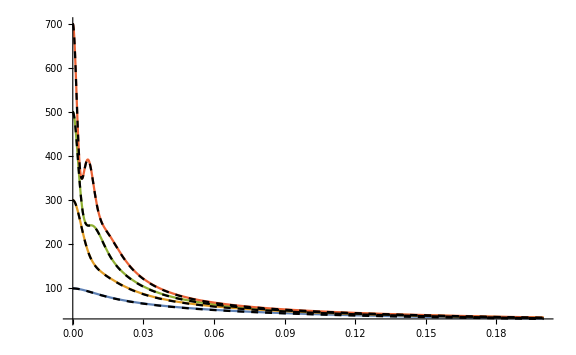

```mathematica
Plot[
{
Re[ada[t]]/.sol100,
Re[ada[t]]/.sol300,
Re[ada[t]]/.sol500,
Re[ada[t]]/.sol700,
Re[ada[t]]/.sol100Test,
Re[ada[t]]/.sol300Test,
Re[ada[t]]/.sol500Test,
Re[ada[t]]/.sol700Test
},
{t, 0, tmax}, PlotRange->All,
ImageSize->Large,
PlotStyle->{,,,,{Black, Dashed}, {Black, Dashed}, {Black, Dashed}, {Black, Dashed}}
]
```

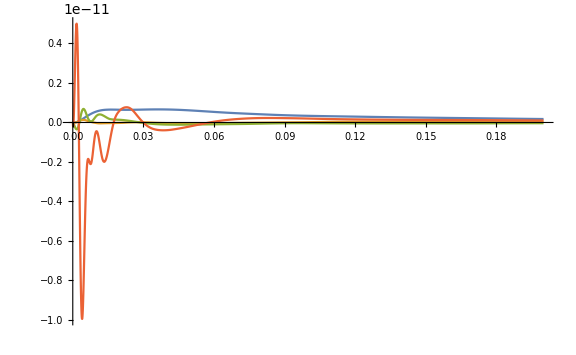

```mathematica
Plot[
{
(*Im[ada[t]]/.sol100,
Im[ada[t]]/.sol300,
Im[ada[t]]/.sol500,
Im[ada[t]]/.sol700,*)
Im[ada[t]]/.sol100Test,
Im[ada[t]]/.sol300Test,
Im[ada[t]]/.sol500Test,
Im[ada[t]]/.sol700Test
},
{t, 0, tmax}, PlotRange->All,
ImageSize->Large,
PlotStyle->{,,,,{Black, Dashed}, {Black, Dashed}, {Black, Dashed}, {Black, Dashed}}
]
```

```mathematica
Q[0.2]/.sol100Test
```

-0.61495-2.419×10^-14 ⅈ

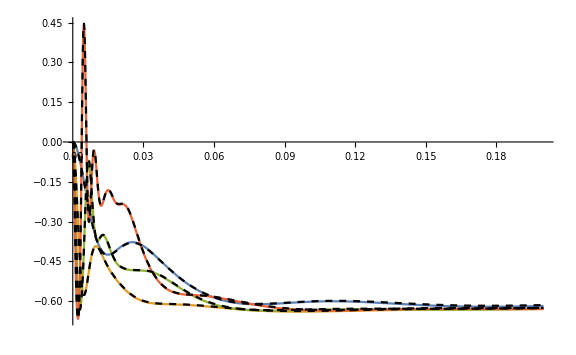

```mathematica
Plot[
{
Re[Q[t]]/.sol100,
Re[Q[t]]/.sol300,
Re[Q[t]]/.sol500,
Re[Q[t]]/.sol700,
Re[Q[t]]/.sol100Test,
Re[Q[t]]/.sol300Test,
Re[Q[t]]/.sol500Test,
Re[Q[t]]/.sol700Test
},
{t, 0, tmax}, PlotRange->All,
ImageSize->Large,
PlotStyle->{,,,,{Black, Dashed}, {Black, Dashed}, {Black, Dashed}, {Black, Dashed}}
]
```

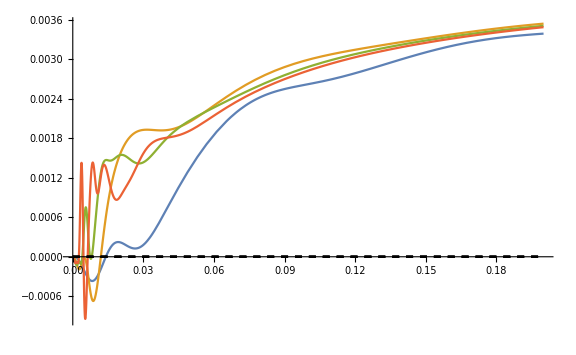

```mathematica
Plot[
{
Im[Q[t]]/.sol100,
Im[Q[t]]/.sol300,
Im[Q[t]]/.sol500,
Im[Q[t]]/.sol700,
Im[Q[t]]/.sol100Test,
Im[Q[t]]/.sol300Test,
Im[Q[t]]/.sol500Test,
Im[Q[t]]/.sol700Test
},
{t, 0, tmax}, PlotRange->All,
ImageSize->Large,
PlotStyle->{,,,,{Black, Dashed}, {Black, Dashed}, {Black, Dashed}, {Black, Dashed}}
]
```

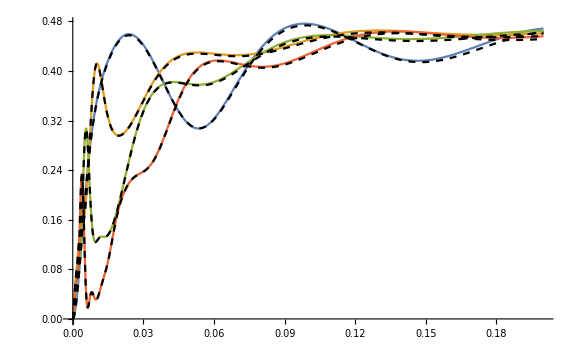

```mathematica
Plot[
{
rotneg1[t, ga, gb, sol100],
rotneg1[t, ga, gb, sol300],
rotneg1[t, ga, gb, sol500],
rotneg1[t, ga, gb, sol700],
rotneg1[t, ga, gb, sol100Test],
rotneg1[t, ga, gb, sol300Test],
rotneg1[t, ga, gb, sol500Test],
rotneg1[t, ga, gb, sol700Test]
},
{t, 0, tmax}, PlotRange->All,
ImageSize->Large,
PlotStyle->{,,,,{Black, Dashed}, {Black, Dashed}, {Black, Dashed}, {Black, Dashed}}
]
```

## Entanglement graphs

### Entanglement graph with same parameters as Fig. 1.13/1.14

```mathematica
(*twoModified[αin_, ga_, gb_, Γ_, U_, γ1in_, tmax_]*)
```

```mathematica
sol = twoModified[√500, 0.412 * 50, 50, 432, 2, 10.0, 0.1]//Chop;
```

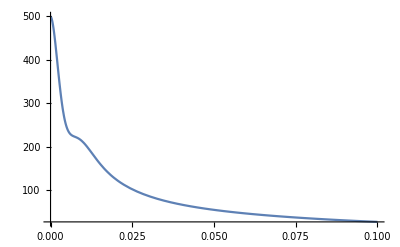

```mathematica
Plot[
ada[t]/.sol,
{t, 0, 0.1}, PlotRange->All
]
```

```mathematica
sol10 = twoModified[√500,  10, 10, 432, 2, 10.0, 0.1];
sol20 = twoModified[√500,  20, 20, 432, 2, 10.0, 0.1];
sol30 = twoModified[√500,  30, 30, 432, 2, 10.0, 0.1];
sol40 = twoModified[√500,  40, 40, 432, 2, 10.0, 0.1];
sol50 = twoModified[√500,  50, 50, 432, 2, 10.0, 0.1];
sol200 = twoModified[√500,  200, 200, 432, 2, 10.0, 0.1];
```

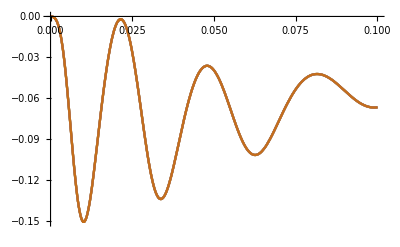

```mathematica
Plot[
{
Chop[Q[t]/.sol10],
Chop[Q[t]/.sol20],
Chop[Q[t]/.sol30],
Chop[Q[t]/.sol40],
Chop[Q[t]/.sol50],
Chop[Q[t]/.sol200]
},
{t, 0,0.1}
]
```

```mathematica
(*rotneg1[t_, g1_, g2_, sol_]*)
```

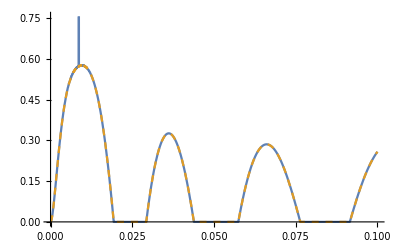

```mathematica
Plot[
{
rotneg1[t, 10, 10, sol10],
rotneg1[t, 200, 200, sol200]
},
{t, 0, 0.1}, PlotStyle->{}
]
```

```mathematica
sol100 = twoModified[√100,  10, 10, 432, 2, 10.0, 0.2];
sol300 = twoModified[√300,  10, 10, 432, 2, 10.0, 0.2];
sol500 = twoModified[√500,  10, 10, 432, 2, 10.0, 0.2];
sol700 = twoModified[√700,  10, 10, 432, 2, 10.0, 0.2];
```

```mathematica
(*rotneg1[t_, g1_, g2_, sol_]*)
```

```mathematica
(*rotneg2[t_, g1_, g2_, sol_]*)
```

```mathematica
sol10 = twoModified[√10,  10, 10, 432, 2, 10.0, 0.2];
sol20 = twoModified[√20,  10, 10, 432, 2, 10.0, 0.2];
sol30 = twoModified[√30,  10, 10, 432, 2, 10.0, 0.2];
sol40 = twoModified[√40,  10, 10, 432, 2, 10.0, 0.2];
sol50 = twoModified[√50,  10, 10, 432, 2, 10.0, 0.2];
sol60 = twoModified[√60,  10, 10, 432, 2, 10.0, 0.2];
sol70 = twoModified[√70,  10, 10, 432, 2, 10.0, 0.2];
sol80 = twoModified[√80,  10, 10, 432, 2, 10.0, 0.2];
sol90 = twoModified[√90,  10, 10, 432, 2, 10.0, 0.2];
sol100 = twoModified[√100,  10, 10, 432, 2, 10.0, 0.2];
sol110 = twoModified[√110,  10, 10, 432, 2, 10.0, 0.2];
sol120 = twoModified[√120,  10, 10, 432, 2, 10.0, 0.2];
sol130 = twoModified[√130,  10, 10, 432, 2, 10.0, 0.2];
sol140 = twoModified[√140,  10, 10, 432, 2, 10.0, 0.2];
sol150 = twoModified[√150,  10, 10, 432, 2, 10.0, 0.2];
sol160 = twoModified[√160,  10, 10, 432, 2, 10.0, 0.2];
sol170 = twoModified[√170,  10, 10, 432, 2, 10.0, 0.2];
sol180 = twoModified[√180,  10, 10, 432, 2, 10.0, 0.2];
sol190 = twoModified[√190,  10, 10, 432, 2, 10.0, 0.2];
```

```mathematica
sol10 = twoModified[√100,  10, 10, 432, 2, 10.0, 0.2];
sol20 = twoModified[√100,  10, 10, 432, 2, 20.0, 0.2];
sol30 = twoModified[√100,  10, 10, 432, 2, 30.0, 0.2];
sol40 = twoModified[√100,  10, 10, 432, 2, 40.0, 0.2];
```

```mathematica
<<MaTeX`
SetOptions[MaTeX,FontSize->12,Magnification->1,"DisplayStyle"->True]
style=Directive[FontFamily->"LM Roman 12",FontSize->10];
cm=72/2.54;
(* http://ksrowell.com/blog-visualizing-data/2012/02/02/optimal-colors-for-graphs/ *)
col1 = RGBColor[57/256, 106/256, 177/256]
col2 = RGBColor[218/256, 124/256, 48/256]
col3= RGBColor[62/256, 150/256, 81/256]
col4 = RGBColor[204/256, 37/256, 41/256]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

RGBColor[Rational[57, 256], Rational[53, 128], Rational[177, 256]]

RGBColor[Rational[109, 128], Rational[31, 64], Rational[3, 16]]

RGBColor[Rational[31, 128], Rational[75, 128], Rational[81, 256]]

RGBColor[Rational[51, 64], Rational[37, 256], Rational[41, 256]]

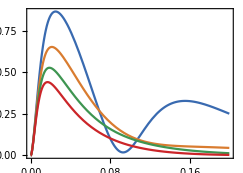

```mathematica
fs1=15;
fs2=10;
fig1 = Plot[
{
rotneg2[t, 10, 10, sol10],
rotneg2[t, 10, 10, sol20],
rotneg2[t, 10, 10, sol30],
rotneg2[t, 10, 10, sol40]
},
{t, 0, 0.2},
ImageSize->8.6cm,
PlotStyle->{col1, col2, col3, col4},
Frame->True,
FrameStyle->BlackFrame,
BaseStyle->style,
AspectRatio->1/1.4,
FrameLabel->{MaTeX["g_b t", ContentPadding->False, FontSize->fs1],
MaTeX["\\mathcal{N}_G", ContentPadding->False, FontSize->fs1]}
];
fig1~Magnify~1
```

### Pumping s_+

```mathematica
<<MaTeX`
SetOptions[MaTeX,FontSize->12,Magnification->1,"DisplayStyle"->True]
style=Directive[FontFamily->"LM Roman 12",FontSize->10];
cm=72/2.54;
(* http://ksrowell.com/blog-visualizing-data/2012/02/02/optimal-colors-for-graphs/ *)
col1 = RGBColor[57/256, 106/256, 177/256]
col2 = RGBColor[218/256, 124/256, 48/256]
col3= RGBColor[62/256, 150/256, 81/256]
col4 = RGBColor[204/256, 37/256, 41/256]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

RGBColor[Rational[57, 256], Rational[53, 128], Rational[177, 256]]

RGBColor[Rational[109, 128], Rational[31, 64], Rational[3, 16]]

RGBColor[Rational[31, 128], Rational[75, 128], Rational[81, 256]]

RGBColor[Rational[51, 64], Rational[37, 256], Rational[41, 256]]

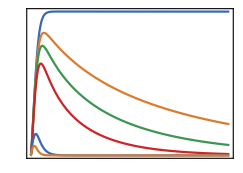

```mathematica
g=10;
Γ=432;
U=2;
(*γ1=0;*)
ain=√200;
sol0=Evaluate[ two3Modified[ain, ain, g, g, U, Γ, 0, 0.2]];
sol5=Evaluate[ two3Modified[ain, ain, g, g, U, Γ, 5, 0.2]];
sol10=Evaluate[ two3Modified[ain, ain, g, g, U, Γ, 10, 0.2]];
sol20=Evaluate[ two3Modified[ain, ain, g, g, U, Γ, 20, 0.2]];
(*sol30=Evaluate[ two3Modified[ain, ain, g, g, U, Γ, 30, 0.2]];

sol40=Evaluate[ two3Modified[ain, ain, g, g, U, Γ, 40, 0.2]];*)
sol200=Evaluate[ two3Modified[ain, ain, g, g, U, Γ, 200, 0.2]];
sol400=Evaluate[ two3Modified[ain, ain, g, g, U, Γ, 400, 0.2]];

fig2=Plot[
{
rotneg2[t, g, g,sol0],
rotneg2[t, g, g,sol5],
rotneg2[t, g, g,sol10],
rotneg2[t, g, g,sol20],
(*rotneg2[t, g, g,sol30],
rotneg2[t, g, g,sol40]*)
rotneg2[t, g, g,sol200],
rotneg2[t, g, g,sol400]
},
{t, 0, 0.2},
PlotRange->All,
ImageSize->8.6cm,
PlotStyle->{col1, col2, col3, col4},
Frame->True,
FrameStyle->BlackFrame,
BaseStyle->style,
AspectRatio->1/1.4,
FrameLabel->{MaTeX["g_b t", ContentPadding->False, FontSize->fs1],
MaTeX["\\mathcal{N}_G", ContentPadding->False, FontSize->fs1]},

FrameTicks->{{{
{0.00, MaTeX["0.0", ContentPadding->False, FontSize->fs2]}, 
{0.2, MaTeX["0.2", ContentPadding->False, FontSize->fs2]}, 
{0.4, MaTeX["0.4", ContentPadding->False, FontSize->fs2]}, 
{0.6, MaTeX["0.6", ContentPadding->False, FontSize->fs2]}, 
{0.8, MaTeX["0.8", ContentPadding->False, FontSize->fs2]}}, None},
{{{0.0, MaTeX["0.00", ContentPadding->False, FontSize->fs2]}, 
{0.05, MaTeX["0.05", ContentPadding->False, FontSize->fs2]},
{0.10, MaTeX["0.10", ContentPadding->False, FontSize->fs2]}, 
{0.15, MaTeX["0.15", ContentPadding->False, FontSize->fs2]},
{0.20, MaTeX["0.20", ContentPadding->False, FontSize->fs2]}
}, None}}


];
fig2~Magnify~1
```

### Parameters mentioned in the paper

```mathematica
two3Modified[ain_, bin_, ga_, gb_, U_, Γ_, γ1in_, tmax_]
```

```mathematica
(4.(60^2+60^2))/(γctest + γ1test)
```

1086.79

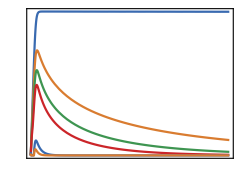

```mathematica
g=60;
Γ=1086.79;
γctest = 15;
U=2;
(*γ1=0;*)
ain=√2500;
γ1test = 11.5;
sol0=Evaluate[ two3Modified[ain, ain, g, g, U, Γ, 0, 0.2]];
sol5=Evaluate[ two3Modified[ain, ain, g, g, U, Γ, 5, 0.2]];
sol11p5=Evaluate[ two3Modified[ain, ain, g, g, U, Γ, 11.5, 0.2]];
sol20=Evaluate[ two3Modified[ain, ain, g, g, U, Γ, 20, 0.2]];
sol200=Evaluate[ two3Modified[ain, ain, g, g, U, Γ, 200, 0.2]];
sol400=Evaluate[ two3Modified[ain, ain, g, g, U, Γ, 400, 0.2]];


fig3=Plot[
{
rotneg2[t, g, g,sol0],
rotneg2[t, g, g,sol5],
rotneg2[t, g, g,sol11p5],
rotneg2[t, g, g,sol20],
rotneg2[t, g, g,sol200],
rotneg2[t, g, g,sol400]
},
{t, 0, 0.2},
PlotRange->All,
ImageSize->8.6cm,
PlotStyle->{col1, col2, col3, col4},
Frame->True,
FrameStyle->BlackFrame,
BaseStyle->style,
AspectRatio->1/1.4,
FrameLabel->{MaTeX["g_b t", ContentPadding->False, FontSize->fs1],
MaTeX["\\mathcal{N}_G", ContentPadding->False, FontSize->fs1]},

FrameTicks->{{{
{0.00, MaTeX["0.0", ContentPadding->False, FontSize->fs2]}, 
{0.4, MaTeX["0.4", ContentPadding->False, FontSize->fs2]}, 
{0.8, MaTeX["0.8", ContentPadding->False, FontSize->fs2]},
{1.2, MaTeX["1.2", ContentPadding->False, FontSize->fs2]},
{1.6, MaTeX["1.6", ContentPadding->False, FontSize->fs2]},
{2.0, MaTeX["2.0", ContentPadding->False, FontSize->fs2]}
}, None},
{{{0.0, MaTeX["0.00", ContentPadding->False, FontSize->fs2]}, 
{0.05, MaTeX["0.05", ContentPadding->False, FontSize->fs2]},
{0.10, MaTeX["0.10", ContentPadding->False, FontSize->fs2]}, 
{0.15, MaTeX["0.15", ContentPadding->False, FontSize->fs2]},
{0.20, MaTeX["0.20", ContentPadding->False, FontSize->fs2]}
}, None}}
];
fig3~Magnify~1
```

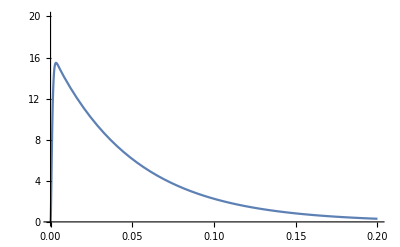

```mathematica
Plot[
Chop[ada[t]/.sol20]
,
{t,0, 0.2},PlotRange->{0, 20}
]
```